```mathematica
lowerbound = 10;
upperbound = 1000;
C1= 2;
C2 = 10;
KR= 12*C1+1/C2;
C11= 2.6;
C21 = 11;
KR1= 12*C11+1/C21;
lambda =10^-7;
cov = 1.84147;
s = 1;
contourPotentialPlot1=ContourPlot[(v1^s+v2^s),{v1,lowerbound,upperbound},{v2,lowerbound,upperbound},PlotRange->All,Contours->25,Axes->False,PlotPoints->30,PlotRangePadding->0,Frame->False,ColorFunction->"DarkRainbow"];

gee =KR^2* ({{1, 0}}).Inverse[Inverse[({{2.09551, cov}, {cov, 2.09551}})]+({{v1, 0}, {0, v2}})].({{1}, {0}})+KR^2*({{0, 1}}).Inverse[Inverse[({{2.09551, cov}, {cov, 2.09551}})]+({{v1, 0}, {0, v2}})].({{0}, {1}});

gee1 =KR1^2* ({{1, 0}}).Inverse[Inverse[({{2.09551, cov}, {cov, 2.09551}})]+({{v1, 0}, {0, v2}})].({{1}, {0}})+KR1^2*({{0, 1}}).Inverse[Inverse[({{2.09551, cov}, {cov, 2.09551}})]+({{v1, 0}, {0, v2}})].({{0}, {1}});
potential1=Plot3D[{gee},{v1,lowerbound,upperbound},{v2,lowerbound,upperbound},PlotRange->Automatic,ClippingStyle->None,MeshFunctions->{#3&},Mesh->35,MeshStyle->Opacity[.5],MeshShading->{{Opacity[.5],Orange}},Lighting->"Neutral"];

level=0;gr=Graphics3D[{Texture[contourPotentialPlot1],EdgeForm[],Polygon[{{lowerbound,lowerbound,level},{upperbound,lowerbound,level},{upperbound,upperbound,level},{lowerbound,upperbound,level}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]},Lighting->"Neutral"];

Show[potential1,gr,PlotRange->All,BoxRatios->{1,1,.6},FaceGrids->{Back,Left}]
```

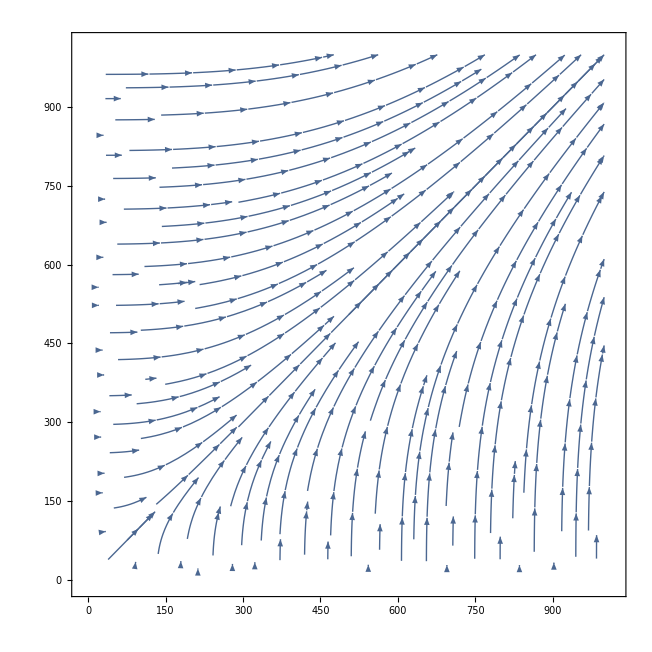

```mathematica
vecfield = Flatten[Grad[Log[gee],{v1,v2}]];
StreamPlot[-vecfield,{v1,lowerbound,upperbound},{v2,lowerbound,upperbound},PlotLegends->Automatic]
```